```mathematica
leqn=Laplacian[u[x,y],{x,y}]==0;
```

```mathematica
Ω=Annulus[{0,0},{3,10},{0,π/2}];
```

```mathematica
innerCond=DirichletCondition[u[x,y]== 2,Norm[{x,y}]==3];
outerCond=DirichletCondition[u[x,y]== 6,Norm[{x,y}]==10];
```

```mathematica
sol=NDSolve[{leqn,innerCond, outerCond},u[x,y],{x,y}∈Ω];
```

```mathematica
Plot3D[Evaluate[u[x,y]/.sol⟦1⟧],{x,y}∈Ω,PlotStyle->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
u[x,y]/.sol[[1]];
```

```mathematica
InterpolatingFunction[…][x,y];
```

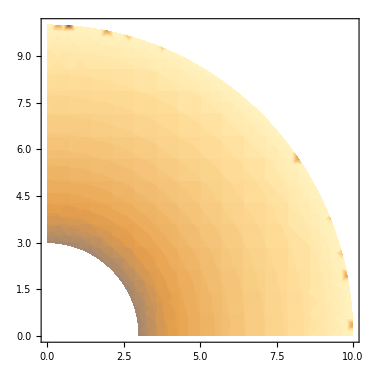

```mathematica
DensityPlot[u[x,y]/.sol[[1]],{x,0.,10.000000000000071},{y,0,10.000000000000068},Mesh->20,MeshFunctions->{#3&}]
```

```mathematica
sol2 = DSolve[{D[r D[u[r],r],r]== 0,u[a]== Ui,u[b]== Uo},u[r],r];
```

```mathematica
u[r]/.sol2[[1]]/.r->√(x^2+y^2)
```

(Uo Log[a]-Ui Log[b]+Ui Log[√(x^2+y^2)]-Uo Log[√(x^2+y^2)])/(Log[a]-Log[b])

```mathematica
N[u[r]/.sol2[[1]]/.r->√(x^2+y^2)/.a->3/.b->10/.Ui->2/.Uo->6]
```

```mathematica
Plot3D[Evaluate[u[r]/.sol2[[1]]/.r->√(x^2+y^2)/.a->3/.b->10/.Ui->2/.Uo->6,{x,y}∈Ω,PlotStyle->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]]
```

-Graphics3D-

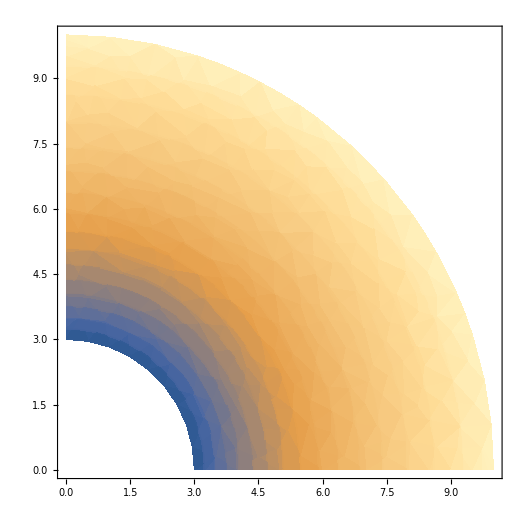

```mathematica
DensityPlot[u[r]/.sol2[[1]]/.r->√(x^2+y^2)/.a->3/.b->10/.Ui->2/.Uo->6,{x,y}∈Ω,Mesh->Automatic,MeshFunctions->{#3&}]
```

```mathematica
Plot3D[Evaluate[ (u[x,y]/.sol[[1]] )- (u[r]/.sol2[[1]]/.r->√(x^2+y^2)/.a->3/.b->10/.Ui->2/.Uo->6),{x,y}∈Ω,PlotStyle->Automatic,PlotRange->All, ColorFunction->"DarkRainbow"]]
```

-Graphics3D-

```mathematica
u[r]/.sol2[[1]]/.r->√(x^2+y^2)/.x->0/.y->4.75/.a->3/.b->10/.Ui->2/.Uo->6
```

3.52672